# Tree Decomposition heuristics

## Heuristics

Tree decomposition uses primary heuristic to pick the nodes to eliminate, and the secondary heuristic to pick between that look equally good to the primary heuristic

```mathematica
SetDirectory[NotebookDirectory[]];
<<Bulatov`treeDecomposition`;

{primary,secondary}=findTreeDecompositionHeuristics;
```

Cost is measured in number of operations needed to evaluate decomposition. Different heuristics can provide orders of magnitude difference in cost.

```mathematica
gridGraph=GridGraph[{5,5}];
decomp=findTreeDecomposition[gridGraph,PrimaryHeuristic->"mincut"];
getTreeCost[decomp]
```

1568

## Evaluating goodness of tree decomposition

```mathematica
(* Graphical model used to predict barley harvest *)
gridGraph=GridGraph[{5,5}];
barleyGraph=Import["./barley.dgf"];
hammingGraph=GraphData[{"Hamming",{3,3}}];

evalCost[g_,h1_,h2_]:=(
decomp=findTreeDecomposition[g,PrimaryHeuristic->h1,SecondaryHeuristic->h2];
getTreeCost[decomp]
);

evalWidth[g_,h1_,h2_]:=(
decomp=findTreeDecomposition[g,PrimaryHeuristic->h1,SecondaryHeuristic->h2];
getTreeWidth[decomp]
);

(* show cost of decomposition for every combination of primary and secondary heuristic *)
costTable[g_]:=(
TableForm[Table[evalCost[g,p,s],{p,primary},{s,secondary}],TableHeadings->{primary,secondary}]
);

widthTable[g_]:=(
TableForm[Table[evalWidth[g,p,s],{p,primary},{s,secondary}],TableHeadings->{primary,secondary}]
);
```

```mathematica
costTable[gridGraph]
```

| accumulation | eccentricity | canonical | random
minfill | 2000 | 8032 | 2216 | 3480
mincut | 1568 | 1568 | 1568 | 1568
canonical | 2216 | 2216 | 2216 | 2216
grid | 1184 | 1184 | 1184 | 1184
eccentricity | 1792 | 1792 | 1792 | 1792
random | 7568 | 5456 | 7656 | 2816

```mathematica
costTable[barleyGraph]
```

| accumulation | eccentricity | canonical | random
minfill | 5072 | 7752 | 6648 | 7896
mincut | 44512 | 44512 | 44512 | 44512
canonical | 667992 | 667992 | 667992 | 667992
grid | 18608 | 23312 | 18928 | 25488
eccentricity | 195856488 | 195856488 | 195856488 | 195856488
random | 79721864 | 44492392 | 51131688 | 650643744

```mathematica
costTable[hammingGraph]
```

| accumulation | eccentricity | canonical | random
minfill | 258176 | 258176 | 258176 | 258176
mincut | 536832 | 536832 | 536832 | 536832
canonical | 1558656 | 1558656 | 1558656 | 1558656
grid | 290944 | 290944 | 290944 | 280704
eccentricity | 1558656 | 1558656 | 1558656 | 1558656
random | 1100416 | 1325696 | 692480 | 1100032

```mathematica
widthTable[gridGraph]
widthTable[barleyGraph]
widthTable[hammingGraph]
```

| accumulation | eccentricity | canonical | random
minfill | 6 | 10 | 6 | 7
mincut | 7 | 7 | 7 | 7
canonical | 6 | 6 | 6 | 6
grid | 6 | 6 | 6 | 6
eccentricity | 7 | 7 | 7 | 7
random | 11 | 10 | 9 | 9

| accumulation | eccentricity | canonical | random
minfill | 8 | 9 | 10 | 9
mincut | 13 | 13 | 13 | 13
canonical | 16 | 16 | 16 | 16
grid | 11 | 11 | 11 | 11
eccentricity | 25 | 25 | 25 | 25
random | 22 | 22 | 22 | 22

| accumulation | eccentricity | canonical | random
minfill | 14 | 14 | 14 | 14
mincut | 17 | 17 | 17 | 17
canonical | 19 | 19 | 19 | 19
grid | 15 | 15 | 15 | 14
eccentricity | 19 | 19 | 19 | 19
random | 17 | 17 | 19 | 17

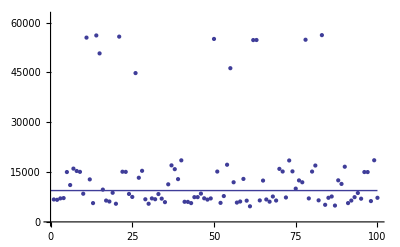

```mathematica
costs=Table[getTreeCost[findTreeDecomposition[barleyGraph,PrimaryHeuristic->"minfill",SecondaryHeuristic->"random"]],{i,1,100}];
getTreeCost[findTreeDecomposition[barleyGraph,PrimaryHeuristic->"minfill",SecondaryHeuristic->"accumulation"]];
plot1=Plot[9432,{x,0,100}];
plot2=ListPlot[costs,PlotRange->{0,Max[costs]*1.1}];
Show[plot1,plot2,PlotRange->{0,Max[costs]*1.1}]
```

## Conclusion

Mincut (p, 2) is better than minfill when graph has a natural binary partition, otherwise it can be very bad. Minfill with accumulation heuristic is best for single run, but still beaten by best random minfill over 20 runs